```mathematica
$Assumptions=0<Subscript[x, 0]<OverBar[Subscript[x, 1]]<OverBar[Subscript[x, 2]]<OverBar[Subscript[x, 3]]&&Subscript[x, 0]<b
```

0<x_0<OverBar[x_1]<OverBar[x_2]<OverBar[x_3]&&x_0<b

## Jeffreys

```mathematica
pj[x_,a_,b_]:=1/x/Log[b/a] Boole[a≤x≤b]
Jeffreys={pj[x,Subscript[x, 0],b],pj[y,Subscript[x, 0],b],pj[z,Subscript[x, 0],b]}
```

{Boole[x_0≤x≤b]/(x Log[b/x_0]),Boole[x_0≤y≤b]/(y Log[b/x_0]),Boole[x_0≤z≤b]/(z Log[b/x_0])}

## Ordered Jeffreys

```mathematica
Z=Integrate[1/(x y z)Boole[a≤x≤y≤z<=b] ,{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->0<a<b]
poj[x_,y_,z_,a_,b_]=1/(x y z)Boole[a≤x≤y≤z<=b]/Z
```

-1/6 Log[a/b]^3

-(6 Boole[a≤x≤y≤z≤b])/(x y z Log[a/b]^3)

```mathematica
𝒟oj=ProbabilityDistribution[poj[x,y,z,a,b],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->0<a<b]
```

ProbabilityDistribution[-(6 Boole[a≤x1≤x2≤x3≤b])/(x1 x2 x3 Log[a/b]^3),{x1,-∞,∞},{x2,-∞,∞},{x3,-∞,∞},Assumptions→0<a<b]

```mathematica
OrderedJeffreys={PDF[MarginalDistribution[𝒟oj,1],x],PDF[MarginalDistribution[𝒟oj,2],y],PDF[MarginalDistribution[𝒟oj,3],z]}/.{a->Subscript[x, 0]}
```

{Piecewise[{{-(3 Log[b/x]^2)/(x Log[x_0/b]^3), -b+x_0<0&&-x+x_0≤0&&b-x>0}, {0, True}}],Piecewise[{{-(6 Log[b/y] Log[y/x_0])/(y Log[x_0/b]^3), -b+x_0<0&&-y+x_0<0&&b-y>0}, {0, True}}],Piecewise[{{-(3 Log[x_0/z]^2)/(z Log[x_0/b]^3), -b+x_0<0&&-z+x_0<0&&b-z≥0}, {0, True}}]}

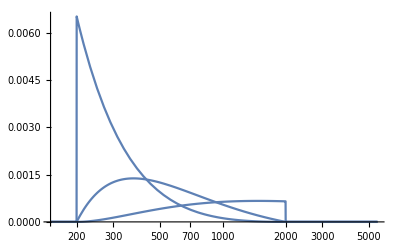

```mathematica
LogLinearPlot[OrderedJeffreys/.{y->x,z->x,Subscript[x, 0]->200,b->2000},{x,150,5500},PlotRange->Full]
```

## ParetoChain

```mathematica
lambda[i_]:=OverBar[Subscript[x, i]]/(OverBar[Subscript[x, i]]-OverBar[Subscript[x, i-1]])/.OverBar[Subscript[x, 0]]->Subscript[x, 0]
expo[i_]:=ExponentialDistribution[lambda[i]]
𝒟u=ProductDistribution[expo[1],expo[2],expo[3]];
```

```mathematica
𝒟x=TransformedDistribution[{Subscript[x, 0] ⅇ^Subscript[u, 1],Subscript[x, 0] ⅇ^(Subscript[u, 1]+Subscript[u, 2]) ,Subscript[x, 0] ⅇ^(Subscript[u, 1]+Subscript[u, 2]+Subscript[u, 3])},{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]}\[Distributed]𝒟u];
Mean[𝒟x]
```

{OverBar[x_1],OverBar[x_2],OverBar[x_3]}

```mathematica
pxyz=PDF[𝒟x,{x,y,z}]//FullSimplify
```

Piecewise[{{(ⅇ^((Log[y/x] OverBar[x_2]^2+(Log[z/y] OverBar[x_1]+Log[x/z] OverBar[x_2]) OverBar[x_3])/((OverBar[x_1]-OverBar[x_2]) (OverBar[x_2]-OverBar[x_3]))) OverBar[x_1] OverBar[x_2] OverBar[x_3] (x/x_0)^(OverBar[x_1]/(-OverBar[x_1]+x_0)))/(x y z (OverBar[x_1]-OverBar[x_2]) (OverBar[x_2]-OverBar[x_3]) (OverBar[x_1]-x_0)), Log[x/x_0]≥0&&Log[x]≤Log[y]&&Log[y]≤Log[z]&&x>0&&y>0&&z>0}, {0, True}}]

```mathematica
num={Subscript[x, 0]->200,OverBar[Subscript[x, 1]]->500,OverBar[Subscript[x, 2]]->1000,OverBar[Subscript[x, 3]]->1500};
𝒟xnum=𝒟x/.num
```

TransformedDistribution[{200 ⅇ^x1,200 ⅇ^(x1+x2),200 ⅇ^(x1+x2+x3)},{x1,x2,x3}\[Distributed]ProductDistribution[ExponentialDistribution[5/3],ExponentialDistribution[2],ExponentialDistribution[3]]]

```mathematica
PC={PDF[MarginalDistribution[𝒟xnum,1],x],PDF[MarginalDistribution[𝒟xnum,2],y],PDF[MarginalDistribution[𝒟xnum,3],z]}
```

{Piecewise[{{(20000 5^(1/3))/(3 x^(8/3)), x>200}, {0, x<200}, {Indeterminate, True}}],Piecewise[{{(40000 (-10+5^(1/3) y^(1/3)))/y^3, y>200}, {0, True}}],Piecewise[{{(30000 (2000-40 z+3 5^(1/3) z^(4/3)))/z^4, z>200}, {0, True}}]}

## Plots

```mathematica
allnum=Append[num,b->5500]
```

{x_0→200,OverBar[x_1]→500,OverBar[x_2]→1000,OverBar[x_3]→1500,b→5500}

```mathematica
JeffreysNumeric=Jeffreys/.allnum;
OrderedJeffreysNumeric=OrderedJeffreys/.allnum;
PCNumeric=PC/.allnum;
```

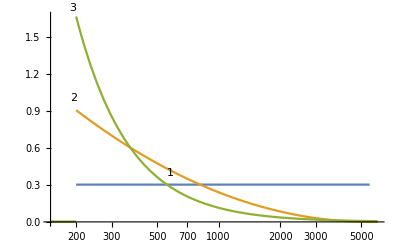

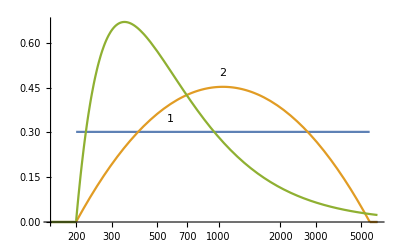

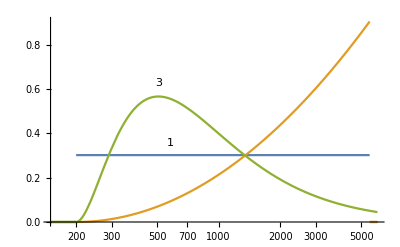

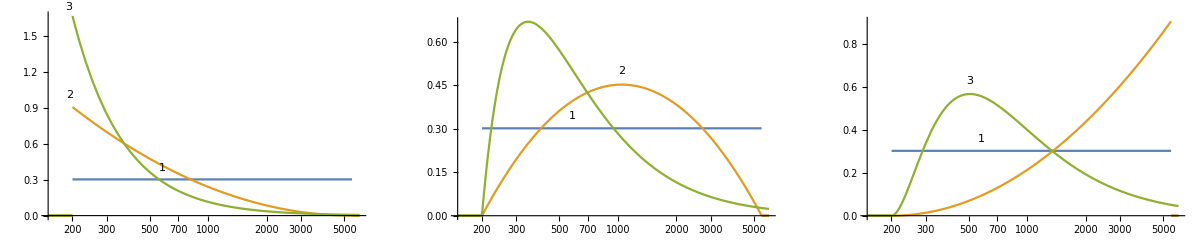

```mathematica
xmin=150;xmax=6000;
P1=LogLinearPlot[{x*JeffreysNumeric[[1]],x*OrderedJeffreysNumeric[[1]],x*PCNumeric[[1]]},{x,xmin,xmax},PlotLabels->Placed[{1,2,3},Above],PlotRange->Full]
P2=LogLinearPlot[{y*JeffreysNumeric[[2]],y*OrderedJeffreysNumeric[[2]],y*PCNumeric[[2]]},{y,xmin,xmax},PlotLabels->Placed[{1,2,3},Above]]
P3=LogLinearPlot[{z*JeffreysNumeric[[3]],z*OrderedJeffreysNumeric[[3]],z*PCNumeric[[3]]},{z,xmin,xmax},PlotLabels->Placed[{1,2,3},Above]]
GraphicsRow[{P1,P2,P3}]
```

```mathematica
JeffreysNumeric
```

{Boole[200≤x≤5500]/(x Log[55/2]),Boole[200≤y≤5500]/(y Log[55/2]),Boole[200≤z≤5500]/(z Log[55/2])}

```mathematica
OrderedJeffreysNumeric//N
```

{Piecewise[{{(0.082412 Log[5500./x]^2)/x, 200.-1. x≤0.&&5500.-1. x>0.}, {0., True}}],Piecewise[{{(0.164824 Log[5500./y] Log[0.005 y])/y, 200.-1. y<0.&&5500.-1. y>0.}, {0., True}}],Piecewise[{{(0.082412 Log[200./z]^2)/z, 200.-1. z<0.&&5500.-1. z≥0.}, {0., True}}]}

```mathematica
PCNumeric//N
```

{Piecewise[{{11399.8/x^(8/3), x>200.}, {0., x<200.}, {Indeterminate, True}}],Piecewise[{{(40000. (-10.+1.70998 y^(1/3)))/y^3, y>200.}, {0., True}}],Piecewise[{{(30000. (2000.-40. z+5.12993 z^(4/3)))/z^4, z>200.}, {0., True}}]}